```mathematica
Integrate[x^2,{x,0,1}]
```

1/3

```mathematica
Integrate[x^2*1/x,{x,0,1}]
```

1/2

```mathematica
2*Integrate[x*(1-x)*1/x,{x,0,1}]
```

1

```mathematica
-x*D[x^2,x]+1/2*x*(1-x)*D[x^2,{x,2}]//FullSimplify
```

x-3 x^2

```mathematica
-x*D[x*(1-x),x]+1/2*x*(1-x)*D[x*(1-x),{x,2}]
```

-(1-2 x) x-(1-x) x

```mathematica
DSolve[{D[f[t],t]==-f[t],f[0]==x0},f,t]
```

{{f→Function[{t},ⅇ^-t x0]}}

```mathematica
DSolve[{D[f[t],t]==x0*Exp[-t]-3*f[t],f[0]==x0^2},f,t]
```

{{f→Function[{t},1/2 ⅇ^(-3 t) x0 (-1+ⅇ^(2 t)+2 x0)]}}

```mathematica
1/2 ⅇ^(-3 t) x0 (-1+ⅇ^(2 t)+2 x0)//FullSimplify
```

```mathematica
pHom = 1/2 ⅇ^(-3 t) x0 (-1+ⅇ^(2 t)+2 x0)
```

1/2 ⅇ^(-3 t) x0 (-1+ⅇ^(2 t)+2 x0)

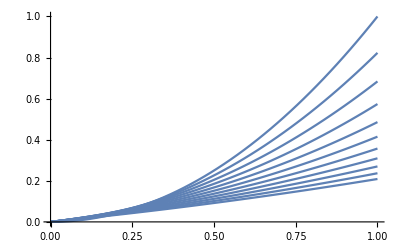

```mathematica
Plot[Table[1/2 ⅇ^(-3 t) x0 (-1+ⅇ^(2 t)+2 x0),{t,0,1,.1}],{x0,0,1}]
```

```mathematica
pHet = 2*(x0*Exp[-t]-pHom)//FullSimplify
```

ⅇ^(-3 t) (1+ⅇ^(2 t)-2 x0) x0

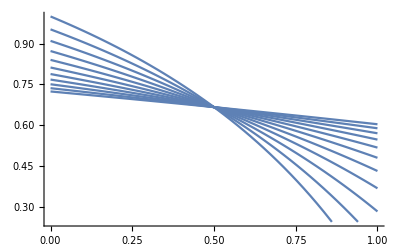

```mathematica
Plot[Table[pHet/(pHet+pHom),{t,0,1,.1}],{x0,0,1}]
```

```mathematica
pHetgHetHom = pHet/(pHet+pHom)//FullSimplify
```

1/(3/2+(-1+2 x0)/(1+ⅇ^(2 t)-2 x0))

```mathematica
pHetAncTable = Table[Table[pHetgHetHom,{x0,.01,.99,.01}],{t,0,1,.1}];
```

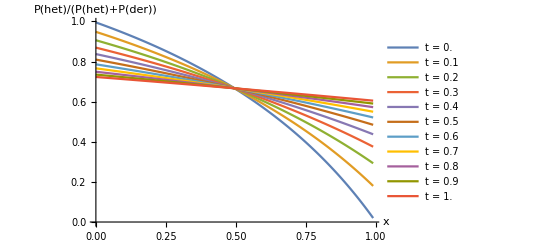

```mathematica
ListLinePlot[pHetAncTable,PlotRange->All,DataRange->{.0,.99},PlotLegends->Table[StringForm["t = ``",ti],{ti,0,1,.1}],AxesLabel->{"x","P(het)/(P(het)+P(der))"}]
```

```mathematica
pHetgHetHom/.{t->.01,x0->.01}
```

0.990051

```mathematica
ExAnc = ⅇ^-t x0/.t->t1
```

ⅇ^-t1 x0

```mathematica
Ex2Anc = 1/2 ⅇ^(-3 t) x0 (-1+ⅇ^(2 t)+2 x0)/.t->t1
```

1/2 ⅇ^(-3 t1) x0 (-1+ⅇ^(2 t1)+2 x0)

```mathematica
ExSplit = x0*Exp[-t1]
```

ⅇ^-t1 x0

```mathematica
Ex2Split = (Exp[-t1]-1/2*Exp[-(3*t1+t2)]-1/2*Exp[-(t1+t2)])*x0+Exp[-(3*t1+t2)]*x0^2
```

(ⅇ^-t1-1/2 ⅇ^(-3 t1-t2)-ⅇ^(-t1-t2)/2) x0+ⅇ^(-3 t1-t2) x0^2

```mathematica
pHetgHetHomSplit = 1-Ex2Split/(2*ExSplit-Ex2Split)//FullSimplify
```

1/(1/2+ⅇ^(2 t1+t2)/(1+ⅇ^(2 t1)-2 x0))

```mathematica
pHetgHetHomAnc = 1-Ex2Anc/(2*ExAnc-Ex2Anc)//FullSimplify
```

1/(3/2+(-1+2 x0)/(1+ⅇ^(2 t1)-2 x0))

```mathematica
pHetSplitTable = Table[Table[pHetgHetHomSplit/.t2->t1-.1,{x0,.01,.99,.01}],{t1,.1,1,.1}];
```

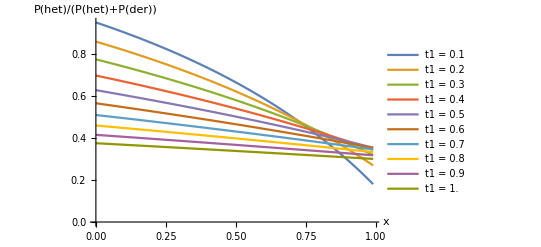

```mathematica
ListLinePlot[pHetSplitTable,PlotRange->All,DataRange->{.0,.99},PlotLegends->Table[StringForm["t1 = ``",ti],{ti,.1,1,.1}],AxesLabel->{"x","P(het)/(P(het)+P(der))"}]
```

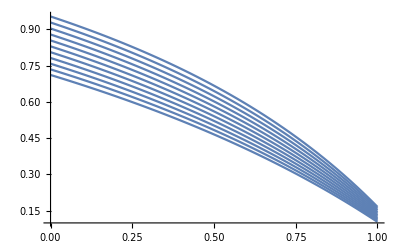

```mathematica
Plot[Table[pHetgHetHomSplit/.t1->0.1,{t2,0,.5,.05}],{x0,0,1}]
```

```mathematica
blah = pHetgHetHomAnc/pHetgHetHomSplit//FullSimplify
```

(1+ⅇ^(2 t1) (1+2 ⅇ^t2)-2 x0)/(1+3 ⅇ^(2 t1)-2 x0)